Numero de supernovas filtradas: 1701

Dimension matriz covarianza: 1701

Dimensiones CovMat: {1701,1701}

Matriz invertida correctamente, dimension: {1701,1701}

Calculando chi cuadrado con matriz de covarianza...

Minimo global: χ^2 = 1878.06 en OmegaM = 0.452, w = -0.7

Puntos dentro de 1σ: 18

Puntos dentro de 2σ: 62

Puntos dentro de 3σ: 98

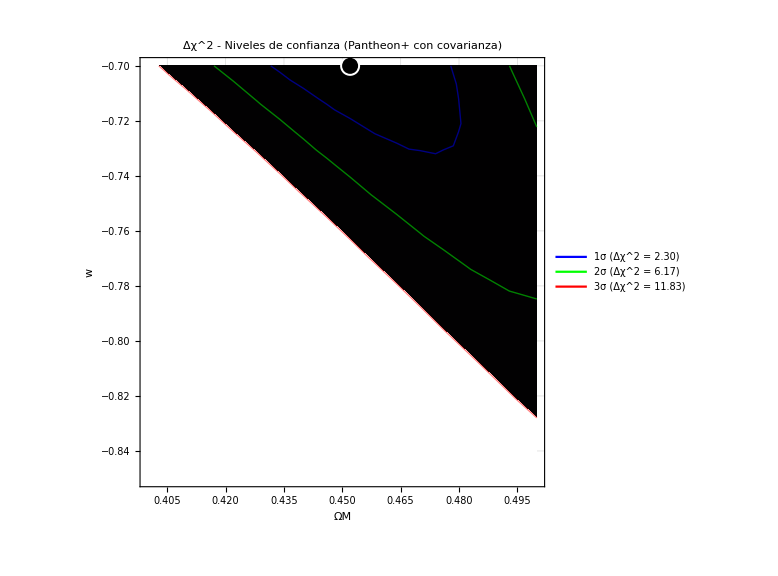

```mathematica
Clear[muTeo,chi2Cov]

H0=70.0;
c=299792.458;

(*Leer datos Pantheon+*)
data=Import["C:\\Users\\joses\\OneDrive\\Documents\\Mathematica\\Pantheon+SH0ES.dat","Table","HeaderLines"->1];

(*Guardar indices originales antes de filtrar para usarlos en la covmat*)
todosNumericos=Select[Range[Length[data]],AllTrue[data[[#,{3,11,12}]],NumericQ]&&data[[#,11]]≠-9&];

lista=data[[todosNumericos,{3,11,12}]];
zObs=lista[[All,1]];
muObs=lista[[All,2]];
n=Length[zObs];
Print["Numero de supernovas filtradas: ",n]

(*Leer matriz de covarianza*)
(*Primera linea=dimension (1701),luego valores uno por linea*)
covRaw=Import["C:\\Users\\joses\\OneDrive\\Documents\\Mathematica\\Pantheon+SH0ES_STAT+SYS.cov","Table"];
nCov=covRaw[[1,1]];
Print["Dimension matriz covarianza: ",nCov]

covVals=Flatten[covRaw[[2;;]]];
CovMat=N[Partition[covVals,nCov]];
Print["Dimensiones CovMat: ",Dimensions[CovMat]]

(*Recortar con los indices correctos*)
CovMatN=CovMat[[todosNumericos,todosNumericos]];
CovInv=Inverse[CovMatN];
Print["Matriz invertida correctamente, dimension: ",Dimensions[CovInv]]

(*Modulo de distancia teorico*)
muTeo[z_,om_,wVal_]:=5*Log10[(1+z)*(c/H0)*NIntegrate[1/Sqrt[om*(1+zp)^3+(1-om)*(1+zp)^(3*(1+wVal))],{zp,0,z},AccuracyGoal->4,PrecisionGoal->4]]+25

(*Chi cuadrado con matriz de covarianza*)
chi2Cov[om_,wVal_]:=Module[{delta},delta=Table[muTeo[zObs[[i]],om,wVal]-muObs[[i]],{i,1,n}];
delta.CovInv.delta]

(*Bucle 2D:OmegaM de 0.2 a 0.5 (paso 0.006),w de-1.3 a-0.7 (paso 0.012)*)
Print["Calculando chi cuadrado con matriz de covarianza..."]
chiContour=Table[{omVal,wVal,chi2Cov[omVal,wVal]},{omVal,0.2,0.5,0.006},{wVal,-1.3,-0.7,0.012}];

chiContourFlat=Flatten[chiContour,1];

(*Minimo y delta chi cuadrado*)
chiMinContour=Min[chiContourFlat[[All,3]]];
minPos=MinimalBy[chiContourFlat,#[[3]]&][[1]];
Print["Minimo global: χ^2 = ",chiMinContour," en OmegaM = ",minPos[[1]],", w = ",minPos[[2]]]

chiDeltaContour={#[[1]],#[[2]],#[[3]]-chiMinContour}&/@chiContourFlat;

(*Niveles de confianza*)
sigma1=Select[chiDeltaContour,#[[3]]≤2.30&];
sigma2=Select[chiDeltaContour,#[[3]]≤6.17&];
sigma3=Select[chiDeltaContour,#[[3]]≤11.83&];
Print["Puntos dentro de 1σ: ",Length[sigma1]]
Print["Puntos dentro de 2σ: ",Length[sigma2]]
Print["Puntos dentro de 3σ: ",Length[sigma3]]

(*Contour plot:eje x=OmegaM,eje y=w*)
ListContourPlot[chiDeltaContour,Contours->{2.30,6.17,11.83},ContourStyle->{{Blue,Thick},{Green,Thick},{Red,Thick}},ColorFunction->"SunsetColors",ContourShading->True,FrameLabel->{{"w",None},{"ΩM",None}},PlotLabel->"Δχ^2 - Niveles de confianza (Pantheon+ con covarianza)",PlotLegends->Placed[LineLegend[{Blue,Green,Red},{"1σ (Δχ^2 = 2.30)","2σ (Δχ^2 = 6.17)","3σ (Δχ^2 = 11.83)"}],Right],Epilog->{White,PointSize[0.025],Point[{minPos[[1]],minPos[[2]]}],Black,
PointSize[0.02],Point[{minPos[[1]],minPos[[2]]}]},Frame->True,

PlotRange->{{0.40,0.50},{-0.85,-0.70}},
GridLines->Automatic,ImageSize->Large]
```